# Data transformation workflows

## Introduction

In this notebook we introduce (Tabular) Data Transformation Workflows through Questions and Answers.

Remark: This notebook is an expanded version of the notebook used in the Wolfram U session [AAv1].

Remark: We use several Wolfram Function Repository (WFR) functions: ExampleDataset and RandomTabularDataset.

Load the paclet

```mathematica
Needs["AntonAntonov`DataReshapers`"]
```

## All questions

### How exciting is this?

Not, but YMMV...

### What are the simplifying assumptions for the family of workflows considered in this tutorial?

We do not consider hard to generalize- or too specialized transformations.

For example, we do not consider:

Data gathering/harvesting

Data ingestion by parsing of, say, XML structures

Date-time specific transformations

Natural text specific transformations

Etc.

### What are the simplifying assumptions about the targeted data and transformations?

Tabular data and collections of tabular data. (E.g. lists of datasets.)

Transformation workflows that can be expressed with a certain "standard" or "well-known" subset of SQL.

The flow chart given below illustrates well the targeted DT.

### Do these workflows apply to other programming languages and/or data systems?

Yes, with the presented DT know-how we target multiple "data science" programming languages.

### Are additional packages needed to run the codes?

Yes and no: depends on the target data transformation system.

Sometimes the WL code uses Wolfram Function Repository functions.

### Are there similar tutorials dedicated to other programming languages or packages?

Yes, many. Both for WL and the rest (Julia/Python/R.)

That said, in this tutorial we use a certain simplified and streamlined data-and-transformations model 
    that allows the development of cross-system, transferable know-how and workflows.

### What are the most important concepts for a newcomer to data wrangling?

Cross tabulation (or contingency matrices)

(Inner) joins

The so called Split-apply-combine pattern

Long form and wide form (or data pivoting)

### How do the considered DT workflows relate to well known Machine Learning (ML) workflows?

Generally speaking, data has to be transformed into formats convenient for the application of ML algorithms.

How much transformation is needed depends a lot on the host system or targeted ML package(s).

For example, WL has extensive ML data on-boarding functions.

("Encoders" and "decoders" that make the use of Neural Networks more streamlined.)

Hence, for using ML in WL less DT is needed.

### How much is WL used?

Approximately 80% we use WL; for illustration purposes we show some of the workflows in other languages.

Run within the same Mathematica presentation notebooks.

## What kind of data?

We concentrate on using data frames (datasets).

More precisely tabular data and simple collections of tabular data.

I.e. in WL -- datasets or lists or associations of datasets.

## What workflows considered?

Here is a flow chart that shows the targeted workflows:

```mathematica
plWorkflows=ImageCrop@Import["https://github.com/antononcube/ConversationalAgents/raw/master/ConceptualDiagrams/Tabular-data-transformation-workflows.jpg"]
```

-Graphics-

## Illustrating example

```mathematica
dfTitanic=ResourceFunction["ExampleDataset"][{"MachineLearning","Titanic"}]
```

```mathematica
ResourceFunction["RecordsSummary"][dfTitanic]
```

{1 passenger class
3rd | 709
1st | 323
2nd | 277,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 28.
Mean | 29.8811
3rd Qu | 39.
Max | 80.
Missing[___] | 263,3 passenger sex
male | 843
female | 466,4 passenger survival
died | 809
survived | 500}

```mathematica
GroupBy[Normal@dfTitanic,#["passenger class"]&,Length[Normal[#]]&]
```

<|1st→323,2nd→277,3rd→709|>

```mathematica
GroupBy[Normal@dfTitanic,#["passenger class"]&,ResourceFunction["CrossTabulate"]@Map[Values,#]⟦All,{3,4}⟧&]
```

<|1st→,2nd→,3rd→|>

```mathematica
ResourceFunction["CrossTabulate"][dfTitanic[All,{"passenger class", "passenger sex"}]]
```

```mathematica
dfTitanic[GroupBy[#["passenger class"]&],GroupBy[#["passenger sex"]&],Length]
```

## Illustrating example 2

#### Column names as data

Take a dataset with time series specified through separate columns and convert into easier to query dataset:

```mathematica
ExampleData[{"Statistics","LakeMeadLevels"},"LongDescription"]
```

Elevation of Lake Mead at Hoover Dam, in feet, in years 1935-2009.  The observation on January of 1935 was missing.

```mathematica
dsLakeData=ResourceFunction["ExampleDataset"][{"Statistics","LakeMeadLevels"}]
```

```mathematica
dfLong=LongFormDataset[dsLakeData,"Year","VariablesTo"->"Month","ValuesTo"->"Elevation"]
dfLong=dfLong[All,Join[#,<|"Month"->DateList[{#Month,{"MonthShort"}}]⟦2⟧|>]&]
```

```mathematica
timeSeriesCollection=GroupBy[Normal@dfLong,#Year&,TimeSeries[Values/@#⟦All,{"Month","Elevation"}⟧]&];
Length[timeSeriesCollection]
```

75

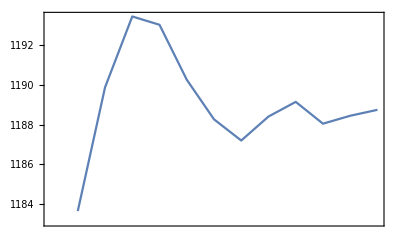
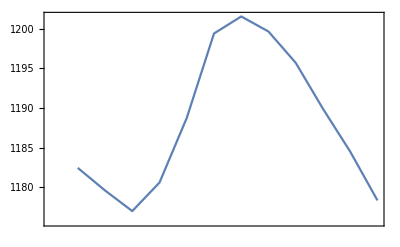
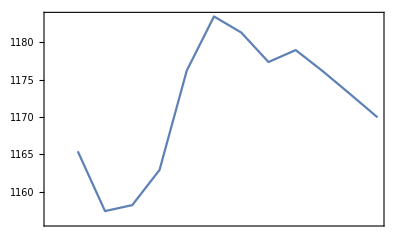
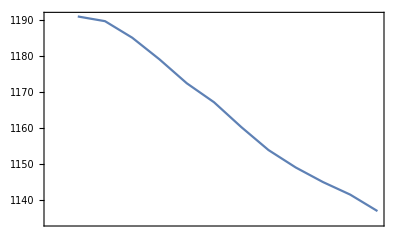
<|1993→-Graphics-,1943→-Graphics-,1939→-Graphics-,1963→-Graphics-|>

```mathematica
SeedRandom[23];
DateListPlot/@RandomSample[timeSeriesCollection,4]
```

### Alternative solution without long form

(This sub-section was not discussed in Wolfram U recording of the “Q&A Introduction” session. It is given in this notebook in order to make a more convenient reference.)

We can apply the Split-Transform-Combine pattern directly without using long form:

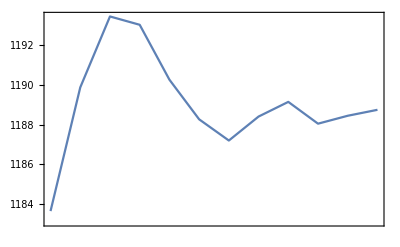
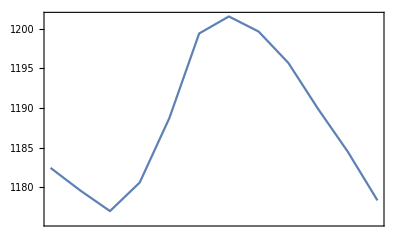
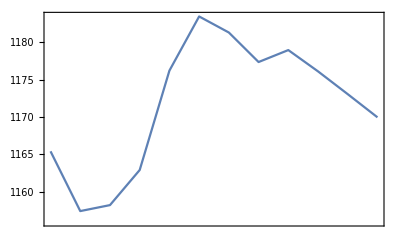
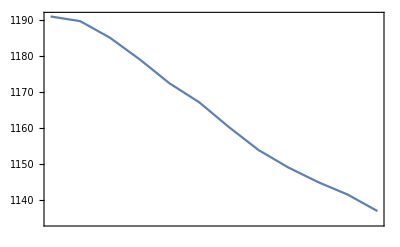
<|1993→-Graphics-,1943→-Graphics-,1939→-Graphics-,1963→-Graphics-|>

```mathematica
SeedRandom[23];
GroupBy[Normal@dsLakeData,#Year&,TimeSeries@Rest@Values@First@#&]//(DateListPlot/@RandomSample[#,4]&)
```

Note that:

In the transformation above we implicitly rely on the sorted order of the month name columns.

Using Rest and First in the third argument given to GroupBy corresponds to the transformations to get the long form.

## References

Wide and narrow data - Wikipedia

[AA1] Anton Antonov, Contingency tables creation examples | Mathematica for prediction algorithms

[AAv1] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #1", (2020), Wolfram channel at YouTube.

[AAv2] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #2", (2020), Wolfram channel at YouTube.

[AAv3] Anton Antonov, "Multi-language Data-Wrangling Conversational Agent", (2021), Wolfram Technology Conference 2020 presentation, Wolfram channel at YouTube.

Related Guides

Data reshaping functions

Related Tech Notes

Long form data transformation

Wide form data transformation

## Metadata

### Categorization

Tech Note

AntonAntonov/DataReshapers

AntonAntonov`DataReshapers`

AntonAntonov/DataReshapers/tutorial/Datatransformationsworkflows

### Keywords

Cross tabulation

Contingency matrix

Contingency table

Data transformation

Long form

Wide form